```mathematica
1、方波的Fourier展开
```

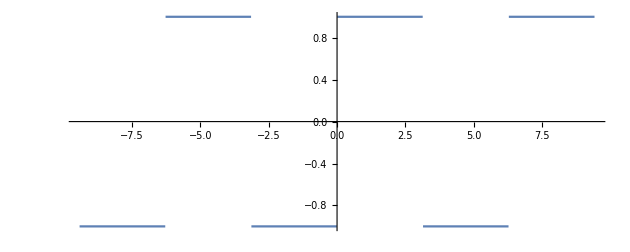

```mathematica
f1=Function[-Sign[Mod[#1,2Pi]-Pi]];
Plot[f1[x],{x,-3Pi,3Pi},AspectRatio->Automatic]
```

```mathematica
f2=Function[ComplexExpand[FourierSeries[f1[#1],#1,#2]]];
Manipulate[f2[x,n],{n,0,20,1}]
```

```mathematica
Manipulate[Plot[{Evaluate[f2[x,n]],f1[x]},{x,-3Pi,3Pi},AspectRatio->Automatic],{n,0,20,1}]
```

```mathematica
Manipulate[Plot[{4/(Pi)*Sum[Sin[(2n-1)*x]/(2n-1),{n,1,m}],f1[x]},{x,-3Pi,3Pi},AspectRatio->Automatic],{m,1,50,1}]
```

```mathematica
2、Fourier最初的例子——金属片上的温度分布问题
```

```mathematica
ContourPlot[
-2*Sum[(-1)^n/n*Sin[n*x]*Sinh[n*y]/Sinh[n*Pi],{n,1,100}],
{x,0,Pi},{y,0,Pi},
ColorFunction->"SolarColors",
Contours->20,
ContourLabels->Function[{x,y,z},Text[Style[z,White,Bold,Medium],{x,y}]]
]
```

```mathematica
Manipulate[ContourPlot[
-2*Sum[(-1)^n/n*Sin[n*x]*Sinh[n*y]/Sinh[n*Pi],{n,1,m}],
{x,0,Pi},{y,0,Pi},
ColorFunction->"SolarColors",
Contours->20,
ContourLabels->Function[{x,y,z},Text[Style[z,White,Bold,Medium],{x,y}]]
],{m,1,50,1}]
```

```mathematica
3、f(x)=x(x∈[-π,π])的Fourier展开
```

```mathematica
f3=Function[Mod[#1+Pi,2Pi]-Pi];
Plot[f3[x],{x,-3Pi,3Pi}]
```

```mathematica
f4=Function[ComplexExpand[FourierSeries[f3[#1],#1,#2]]];
Manipulate[f4[x,n],{n,0,20,1}]
```

```mathematica
Manipulate[Plot[{Evaluate[f4[x,n]],f3[x]},{x,-3Pi,3Pi}],{n,0,20,1}]
```

```mathematica
Manipulate[Plot[{Sum[2*(-1)^(n+1)*Sin[n*x]/n,{n,1,m}],f3[x]},{x,-3Pi,3Pi}],{m,1,50,1}]
```

```mathematica
4、f(x)=e^x(x∈[0,2π])的Fourier展开
```

```mathematica
f5=Function[Mod[#1+Pi,2Pi]-Pi];
f6=Function[Piecewise[{{E^(f5[#1]),f5[#1]>0},{E^(f5[#1]+2Pi),f5[#1]<0}}]];
Plot[f6[x],{x,-3Pi,3Pi}]
```

```mathematica
f7=Function[ComplexExpand[FourierSeries[f6[#1],#1,#2]]];
Manipulate[f7[x,n],{n,0,20,1}]
```

```mathematica
Plot[{Evaluate[f7[x,11]],f6[x]},{x,-3Pi,3Pi}]
```

```mathematica
5、f(x)=|x|(x∈[-π,π])的Fourier展开
```

```mathematica
f8=Function[Abs[f5[#1]]];
Plot[f8[x],{x,-3Pi,3Pi},AspectRatio->Automatic]
```

```mathematica
f9=Function[ComplexExpand[FourierSeries[f8[#1],#1,#2]]];
Manipulate[f9[x,n],{n,0,20,1}]
```

```mathematica
Plot[{Evaluate[f9[x,3]],f8[x]},{x,-3Pi,3Pi},AspectRatio->Automatic]
```